## Favorable pressure gradient base ﬂow computations

See baseflow.tex write up for the background on this notebook.

## The nondimensional, compressible potential flow equation

```mathematica
<<"Utilities`CleanSlate`";
CleanSlate[];
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 777 Kb

```mathematica
Needs["VectorAnalysis`"];
SetCoordinates[Cylindrical];
With[{f=phi[Rr]},With[{gf=Simplify[Grad[f]],lf=Simplify[Laplacian[f]]},With[{gf2=Simplify[DotProduct[gf,gf]]},lf-(Ma^2/2) DotProduct[gf,Grad[gf2]]-(gamma0-1)(Ma^2/2)(gf2-1)lf]]];
Collect[%,{phi''[Rr],phi'[Rr],phi[Rr]}];
Map[Simplify,%];
resphi=%
```

((2+(-1+gamma0) Ma^2) phi'[Rr])/(2 Rr)-((-1+gamma0) Ma^2 phi'[Rr]^3)/(2 Rr)-1/2 (-2-(-1+gamma0) Ma^2+(1+gamma0) Ma^2 phi'[Rr]^2) phi''[Rr]

```mathematica
r resphi/.{gamma0->γ0,phi''[Rr]->u'[r],phi'[Rr]->u[r],Rr->r};
resu=%//Simplify
```

1/2 ((2+Ma^2 (-1+γ0)) u[r]-Ma^2 (-1+γ0) u[r]^3+r (2+Ma^2 (-1+γ0)) u'[r]-Ma^2 r (1+γ0) u[r]^2 u'[r])

## The sub - and supersonic radially - symmetric nozzle problems

First, some numerical solutions to double check what' s presented in the write up.

Subsonic case with nozzle from right-to-left.  We want the strictly negative u to decrease as one travels radially inward so one would, from that frame, observe an accelerating flow.

Pushing u[2] much harder than what is done below leads to a choked, sonic flow and NDSolve can no longer handle the problem.

u[r]^2 (u[r]+6 r u'[r])==6 (u[r]+r u'[r])

InterpolatingFunction[{{1.,2.}},<>][r]

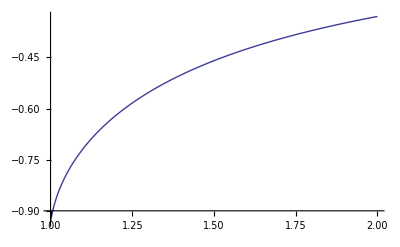

```mathematica
resu==0/.{Ma->1,γ0->7/5}//Simplify
u[r]/.NDSolve[{%,u[2]==-33/100},u,{r,1,2}]//First
Plot[%,{r,1,2},PlotRange->Full]
```

However, instead of specifying a subsonic inflow one can set a nearly choked outflow at u[1] and then take the domain as large as desired:

u[r]^2 (u[r]+6 r u'[r])==6 (u[r]+r u'[r])

InterpolatingFunction[{{1.,4.}},<>][r]

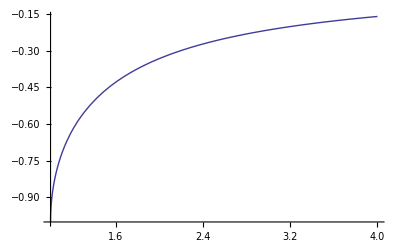

```mathematica
resu==0/.{Ma->1,γ0->7/5}//Simplify
u[r]/.NDSolve[{%,u[1]==-0.9999},u,{r,1,4}]//First
Plot[%,{r,1,4},PlotRange->Full]
```

Supersonic case with nozzle from left-to-right.  We want the strictly positive u to increase as one travels radially outward so one would, from that frame, observe an accelerating flow.

u[r]^2 (u[r]+6 r u'[r])==6 (u[r]+r u'[r])

InterpolatingFunction[{{1.,10.}},<>][r]

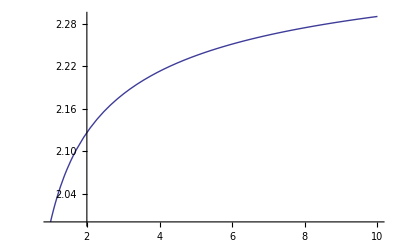

```mathematica
resu==0/.{Ma->1,γ0->7/5}//Simplify
u[r]/.NDSolve[{%,u[1]==2},u,{r,1,10}]//First
Plot[%,{r,1,10},PlotRange->Full]
```